```mathematica
n = 2; (* dimension *)
k = 10; (* number of points *)
r = 5; (* radius *)


(* picking the boundary points at random *)
RandomBounds = RandomInteger[{0, 20}, {2, n}]; 
LowerLeftBound = Map[Min, Transpose[RandomBounds]];    
UpperRightBound = Map[Max, Transpose[RandomBounds]];
{LowerLeftBound, UpperRightBound}    

(*
LowerLeftBound = {0, 0};
UpperRightBound = {10, 10};
*)
```

{{1,2},{11,8}}

```mathematica
(* TORUS *)
(*
SimplicialComplex = {{1},{2},{3},{4},{5},{6},{7},{8},{9},
{1,2},{1,4},{1,3},{1,5},{1,7},{1,8},{2,6},{2,3},{2,9},{2,8},{2,4},{3,5},{3,6},{3,7},{3,9},{4,5},{4,6},{4,7},{4,9},{5,6},{5,8},{5,9},{6,7},{6,8},{7,8},{7,9},{8,9},
{1,2,4},{2,4,6},{2,3,6},{3,6,7},{1,3,7},{1,4,7},{4,5,6},{5,6,8},{6,7,8},{7,8,9},{4,7,9},{4,5,9},{1,5,8},{1,2,8},{2,8,9},{2,3,9},{3,5,9},{1,3,5}}
CardSn = {{0,9},{1,27},{2,18},{3,0},{4,0},{5,0},{6,0},{7,0},{8,0}};
*)

(* KLEIN_BOTTLE *)
(*
SimplicialComplex = {{1},{2},{3},{4},{5},{6},{7},{8},{9},
{1,2},{1,4},{1,3},{1,5},{1,6},{1,9},{2,6},{2,3},{2,7},{2,8},{2,5},{3,5},{3,8},{3,7},{3,9},{4,5},{4,6},{4,7},{4,9},{4,8},{5,7},{5,8},{6,7},{6,8},{6,9},{7,9},{8,9},
{1,2,6},{1,4,6},{2,3,7},{2,6,7},{1,3,5},{3,5,7},{4,5,8},{4,6,8},{6,7,9},{6,8,9},{4,7,9},{4,5,7},{1,5,2},{2,5,8},{3,8,9},{2,3,8},{1,3,9},{1,4,9}}
CardSn = {{0,9},{1,27},{2,18},{3,0},{4,0},{5,0},{6,0},{7,0},{8,0}};
*)

(* 2-SPHERE *)
(*
SimplicialComplex ={{1},{2},{3},{4},
{1,3},{1,2},{1,4},{2,3},{2,4},{3,4},
{1,2,4},{2,3,4},{1,3,4},{1,3,2}}
CardSn = {{0,4},{1,6},{2,4},{3,0}}
*)

(* PROJECTIVE PLANE *)
(*
SimplicialComplex = {{1},{2},{3},{4},{5},{6},
{1,2},{1,3},{1,4},{1,5},{1,6},{2,3},{2,4},{2,5},{2,6},{3,4},{3,5},{3,6},{4,5},{4,6},{5,6},
{1,2,5},{1,2,6},{1,3,4},{1,3,6},{1,4,5},{2,3,4},{2,3,5},{2,4,6},{3,5,6},{4,5,6}}
CardSn = {{0,6},{1,15},{2,10},{3,0},{4,0},{5,0}}
*)
```

```mathematica
SeedRandom[42];

GenerateRandomSet[n_, k_, LowerLeft_, UpperRight_] := Module[
    {Points},
    If[Length[LowerLeft] != n || Length[UpperRight] != n,
        Return["Boundary points should be of given length n."]
    ];
    (* generating k points R^n *)
    Points = Table[
        RandomInteger[{LowerLeft[[i]], UpperRight[[i]]}], {i, n}, {j, k}
    ];
    Transpose[Points]
];
```

```mathematica
GenerateDistanceMatrix[points_, r_] := Module[
  {n = Length[points], adjacency},
  adjacency = Table[
    EuclideanDistance[points[[i]], points[[j]]],
    {i, n}, {j, n}
  ];
  adjacency
];
```

```mathematica
(* a function for constructing the Vietoris-Rips complex with the following arguments:
- points_: a list of points which act as vertices for the complex
- distanceMatrix_: a matrix of precomputed Euclidean distances between coordinate pairs
- r_: the given radius parameter
- maxDim_: a rough estimate of the dimension up to which the calculations will be sensible
for the user input, it can obviously be increased but it is taken as an argument to avoid
redundant calculations for simpler examples *)

VietorisRipsComplex[points_, distanceMatrix_, r_, maxDim_ : 10] := Module[{
    n = Length[points],
    dims, k, combos
  },
  
  (* validating input *)
  If[Length[points] == 0, Return[Association[]]];
  
  (* using a dictionary to store k-simplices to speed up later calls *)
  dims = Association[];
  
  (* dim0 = all singletons {i} for i in 1..n *)
  dims["dim0"] = Table[{i}, {i, n}];
  
  (* for each dimension from 1 up to maxDim gathering all subsets 
     of size (k+1) whose pairwise distances are <= r. *)
  Do[
    combos = Subsets[ Range[n], {k + 1} ];
    combos = Select[
      combos,
      AllTrue[Subsets[#, {2}], distanceMatrix[[#[[1]], #[[2]]]] <= r &] &
    ];
    dims["dim" <> ToString[k]] = combos;
    ,
    {k, 1, maxDim}
  ];
  Return[dims];
];
```

```mathematica
InputPoints = GenerateRandomSet[n, k, LowerLeftBound, UpperRightBound]
(* Edges = GenerateDistanceMatrix[InputPoints, r] *)

SimplicialComplex = VietorisRipsComplex[InputPoints, Edges, r, 4];
Print["Simplices in each dimension: "]
SimplicialComplex
```

{{10,2},{6,2},{8,4},{5,5},{5,2},{9,2},{11,7},{3,6},{2,6},{3,3}}

Simplices in each dimension:

<|dim0→{{1},{2},{3},{4},{5},{6},{7},{8},{9},{10}},dim1→{{1,2},{1,8},{1,10},{2,4},{2,5},{2,8},{2,10},{3,4},{3,5},{3,6},{3,7},{3,8},{4,5},{4,6},{4,7},{4,8},{5,7},{5,8},{6,8},{8,9},{8,10}},dim2→{{1,2,8},{1,2,10},{1,8,10},{2,4,5},{2,4,8},{2,5,8},{2,8,10},{3,4,5},{3,4,6},{3,4,7},{3,4,8},{3,5,7},{3,5,8},{3,6,8},{4,5,7},{4,5,8},{4,6,8}},dim3→{{1,2,8,10},{2,4,5,8},{3,4,5,7},{3,4,5,8},{3,4,6,8}},dim4→{}|>

```mathematica
`
```

```mathematica
DrawBalls[showNeighborhoods_, vertices_, r_, showIndices_] :=
  If[
    showNeighborhoods,
    Table[
      {Hue[0.9, 0.9, 0.4, 0.1], Disk[vertices[[i]], r/2]},
      {i, showIndices}
    ],
    {}
  ];

DrawOneSimplices[vertices_, distanceMatrix_, r_, showIndices_] := 
  Table[
    If[
    (* checking the Vietoris-Rips condition for distances between each pair of points *)
      i < j &&
      MemberQ[showIndices, i] &&
      MemberQ[showIndices, j] &&
      distanceMatrix[[i, j]] <= r,
      {AbsoluteThickness[1.8], Black, Line[{vertices[[i]], vertices[[j]]}]},
      {}
    ],
    {i, Length[vertices]}, {j, i + 1, Length[vertices]}
  ] // Flatten;

DrawTwoSimplices[vertices_, distanceMatrix_, r_, showIndices_] := 
  Table[
    If[
    (* checking the Vietoris-Rips condition for distances between each triple of points *)
      distanceMatrix[[i, j]] <= r &&
      distanceMatrix[[i, k]] <= r &&
      distanceMatrix[[j, k]] <= r &&
      MemberQ[showIndices, i] &&
      MemberQ[showIndices, j] &&
      MemberQ[showIndices, k],
      {
        Hue[0.6, 0.9, 0.5, 0.1],
        EdgeForm[Black],
        Polygon[{vertices[[i]], vertices[[j]], vertices[[k]]}]
      },
      {}
    ],
    {i, Length[vertices]}, {j, i + 1, Length[vertices]}, {k, j + 1, Length[vertices]}
  ] // Flatten;
```

```mathematica
ManipulateComplex[vertices_, distanceMatrix_, R_] := 
  Manipulate[
    Graphics[
      Flatten[
        {
          DrawBalls[showNeighborhoods, vertices, r, selectedPoints],
          DrawOneSimplices[vertices, distanceMatrix, r, selectedPoints],
          DrawTwoSimplices[vertices, distanceMatrix, r, selectedPoints],
          
          (* drawing vertices as points *)
          Table[{Black, Point[vertices[[i]]]}, {i, selectedPoints}]
          (* Table[{Black, PointSize[0.01], Point[vertices[[i]]]}, {i, selectedPoints}] *)
        }
      ],
      PlotRange -> {
        {LowerLeftBound[[1]] - R, UpperRightBound[[1]] + R},
        {LowerLeftBound[[2]] - R, UpperRightBound[[2]] + R}
      },
      PlotRangeClipping -> False,
      ImageSize -> 600
    ],
    
    {{showNeighborhoods, True, "Draw neighborhoods"}, {True, False}},
    {{r, R, "Neighborhood radius"}, 0, R + 5, Appearance -> "Labeled"},
    {{selectedPoints, Range[Length[vertices]], "Points to show"},
      Range[Length[vertices]],
      ControlType -> CheckboxBar
    },
    Delimiter,
    Style["Vietoris-Rips simplicial complex", 12, Bold]
  ];

ManipulateComplex[InputPoints, Edges, r]
```

```mathematica
(* counting simplices of each dimension using the previously implemented dictionary *)
CountSimplices[complex_] := Module[
  {dimKeys, counts},
  
  dimKeys = Keys[complex];
  counts = Table[
    {StringReplace[dim, "dim" -> ""], Length[complex[dim]]},
    {dim, dimKeys}
  ];

  Dataset[counts]
];
```

```mathematica
NumberOfSimplices = CountSimplices[SimplicialComplex];

(* filling the cardinality array for each dimension with existing simplices *)
CardSn = Normal[NumberOfSimplices];
CardSn
NumberOfSimplices
```

{{0,10},{1,21},{2,17},{3,5},{4,0}}

```mathematica
(* a function for drawing an indicative graph representation
of the simplicial complex based on the vertices and edges *)

GenerateGraph[complex_, n_] := Module[
  {edges, vertices},
  
  edges = complex["dim1"];
  vertices = Range[n];
  
  Graph[
    vertices,
    UndirectedEdge @@@ edges,
    VertexLabels -> Table[i -> Placed[i, Center], {i, vertices}],
    VertexSize -> 0.5
  ]
];
```

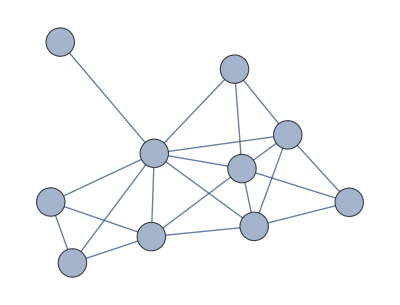

```mathematica
VisualizeComplex = GenerateGraph[SimplicialComplex, Length[InputPoints]]
```

```mathematica
(* harvesting the connected components of the graph to later obtain 
the 0-th Betti number and avoid unnecessary matrix calculations *)

ShowConnectedComponents[complex_] := Module[
  {edges, vertices, graph},
  
  edges = complex["dim1"];
  vertices = Range[Length[complex["dim0"]]];
  
  graph = Graph[
    vertices,
    UndirectedEdge @@@ edges
  ];
  
  ConnectedComponents[graph]
];
```

```mathematica
ComplexConnectedComponents = ShowConnectedComponents[SimplicialComplex]
Betti0 = Length[ComplexConnectedComponents]
```

{{1,2,3,4,5,6,7,8,9,10}}

1

```mathematica
(* counting dimensions in which any simplices in the simplicial complex exist,
so that there are no redundant calculations for homology groups that are trivial *)

(* for example, if there are simplices only up to dimension 3, homology groups 
of higher dimensions needn't be calculated since they will always be 0*)

CountPotentiallyNontrivialHomologies[complex_] := Module[
  {counts},
  
  counts = Count[Length[complex[#]] > 0 & /@ Keys[complex], True];
  counts
];
```

```mathematica
PotentiallyNontrivialHomologies = CountPotentiallyNontrivialHomologies[SimplicialComplex];
PotentiallyNontrivialHomologies
```

4

```mathematica
(* a helper function used to transform border matrices into column echelon form, 
since the built-in Mathematica function RowReduceAlternative[matrix, Modulus -> 2]
does not seem to work for non-square border matrices *)

ColumnEchelonForm[matrix_] := Module[
  {mat = matrix, rows, cols},
  {rows, cols} = Dimensions[mat];
  
  (* helper function to find the leading index in a column *)
  LeadingIndex[col_] := FirstPosition[col, 1, ∞][[1]];
  
  (* helper function to check whether the column is 0 *)
  IsZeroColumn[col_] := AllTrue[col, # == 0 &];
  
  Do[
    (* finding column with the minimum leading index among remaining columns *)
    Module[{
      remainingCols = Range[j, cols],
      leadingIndices,
      minLeadIndex,
      colWithMinLead
    },
      (* calculating leading indices for remaining columns *)
      leadingIndices = Map[LeadingIndex[mat[[All, #]]] &, remainingCols];
      
      (* finding the minimum leading index and its column *)
      minLeadIndex = Min[leadingIndices];
      
      (* if we find a non-zero column *)
      If[minLeadIndex < ∞,
        (* locate the first column with minimum leading index *)
        colWithMinLead = remainingCols[[FirstPosition[leadingIndices, minLeadIndex][[1]]]];
        
        (* swap if not already in position *)
        If[colWithMinLead != j,
          mat[[All, {j, colWithMinLead}]] = mat[[All, {colWithMinLead, j}]];
        ];
        
        (* add column j to all other columns that have 1 in the same leading position *)
        Do[
          If[k != j && mat[[minLeadIndex, k]] == 1,
            mat[[All, k]] = Mod[mat[[All, k]] + mat[[All, j]], 2];
          ],
          {k, j + 1, cols}
        ];
      ];
    ];
    ,
    {j, 1, cols}
  ];
  
  (* moving all zero columns to the end *)
  Module[{
    nonZeroCols = Select[Range[cols], !IsZeroColumn[mat[[All, #]]] &],
    zeroCols = Select[Range[cols], IsZeroColumn[mat[[All, #]]] &]
  },
    mat = mat[[All, Join[nonZeroCols, zeroCols]]];
  ];
  
  mat
]
```

```mathematica
(* a function for constructing the simplicial complex border operator matrix for a given dimension *)
BorderMatrix[complex_, k_] := Module[
  {
    kSimplices, (* k-simplices *)  
    kMinusOneSimplices, (*(k-1)-simplices *)
    matrix, columnLabels, rowLabels, rank
  },
  
  (* indentifying the k-simplices and the (k-1)-simplices *)
  kSimplices = complex["dim" <> ToString[k]];
  kMinusOneSimplices = complex["dim" <> ToString[k - 1]];
  
  (* constructing the 0–1 boundary matrix based on incidence *)
  matrix = Table[
    If[SubsetQ[kSimplices[[j]], kMinusOneSimplices[[i]]], 1, 0],
    {i, 1, Length[kMinusOneSimplices]},
    {j, 1, Length[kSimplices]}
  ];
  
  matrix = ColumnEchelonForm[matrix];
  
  (* building string labels for row and column simplices *)
  columnLabels = Map[
    (StringJoin["〈", Riffle[ToString /@ #, ","], "〉"] &),
    kSimplices
  ];
  rowLabels = Map[
    (StringJoin["〈", Riffle[ToString /@ #, ","], "〉"] &),
    kMinusOneSimplices
  ];
  
  rank = MatrixRank[matrix];
  
  <|
    "RawMatrix" -> matrix,
    "LabeledMatrix" -> MatrixForm[
      matrix,
      TableHeadings -> {rowLabels, columnLabels}
    ],
    "Rank" -> rank,
    "k-Simplices" -> kMinusOneSimplices,
    "(k-1)-Simplices" -> kSimplices
  |>
];
```

```mathematica
result = BorderMatrix[SimplicialComplex, 1];
result["LabeledMatrix"]
Print["Matrix rank: ", result["Rank"]]
```

( | 〈1,2〉 | 〈1,8〉 | 〈1,10〉 | 〈2,4〉 | 〈2,5〉 | 〈2,8〉 | 〈2,10〉 | 〈3,4〉 | 〈3,5〉 | 〈3,6〉 | 〈3,7〉 | 〈3,8〉 | 〈4,5〉 | 〈4,6〉 | 〈4,7〉 | 〈4,8〉 | 〈5,7〉 | 〈5,8〉 | 〈6,8〉 | 〈8,9〉 | 〈8,10〉
〈1〉 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
〈2〉 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
〈3〉 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
〈4〉 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
〈5〉 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
〈6〉 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
〈7〉 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
〈8〉 | 0 | 1 | 0 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
〈9〉 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
〈10〉 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

Matrix rank: 9

```mathematica
(* an array which stores the ranks of the matrices for later Betti number calculations *)
ranks = {}; 

(* a function to output border matrices which make sense for the given simplicial complex *)

Do[
  With[{res = BorderMatrix[SimplicialComplex, k]},
    Print[Indexed[δ, k], ": "];
    Print[res["LabeledMatrix"]];
    Print["Matrix rank: ", res["Rank"]];
    AppendTo[ranks, res["Rank"]]; 
  ],
  (* may as well start from 1 because we have already precomputed Betti0 *)
  {k, 1, PotentiallyNontrivialHomologies - 1} 
];
```

δ1:

( | 〈1,2〉 | 〈1,8〉 | 〈1,10〉 | 〈2,4〉 | 〈2,5〉 | 〈2,8〉 | 〈2,10〉 | 〈3,4〉 | 〈3,5〉 | 〈3,6〉 | 〈3,7〉 | 〈3,8〉 | 〈4,5〉 | 〈4,6〉 | 〈4,7〉 | 〈4,8〉 | 〈5,7〉 | 〈5,8〉 | 〈6,8〉 | 〈8,9〉 | 〈8,10〉
〈1〉 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
〈2〉 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
〈3〉 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
〈4〉 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
〈5〉 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
〈6〉 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
〈7〉 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
〈8〉 | 0 | 1 | 0 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
〈9〉 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
〈10〉 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

Matrix rank: 9

δ2:

( | 〈1,2,8〉 | 〈1,2,10〉 | 〈1,8,10〉 | 〈2,4,5〉 | 〈2,4,8〉 | 〈2,5,8〉 | 〈2,8,10〉 | 〈3,4,5〉 | 〈3,4,6〉 | 〈3,4,7〉 | 〈3,4,8〉 | 〈3,5,7〉 | 〈3,5,8〉 | 〈3,6,8〉 | 〈4,5,7〉 | 〈4,5,8〉 | 〈4,6,8〉
〈1,2〉 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
〈1,8〉 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
〈1,10〉 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
〈2,4〉 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
〈2,5〉 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
〈2,8〉 | 1 | 1 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
〈2,10〉 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
〈3,4〉 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
〈3,5〉 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
〈3,6〉 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
〈3,7〉 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
〈3,8〉 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
〈4,5〉 | 0 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
〈4,6〉 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
〈4,7〉 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
〈4,8〉 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0
〈5,7〉 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
〈5,8〉 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0
〈6,8〉 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
〈8,9〉 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
〈8,10〉 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

Matrix rank: 12

δ3:

( | 〈1,2,8,10〉 | 〈2,4,5,8〉 | 〈3,4,5,7〉 | 〈3,4,5,8〉 | 〈3,4,6,8〉
〈1,2,8〉 | 1 | 0 | 0 | 0 | 0
〈1,2,10〉 | 1 | 0 | 0 | 0 | 0
〈1,8,10〉 | 1 | 0 | 0 | 0 | 0
〈2,4,5〉 | 0 | 1 | 0 | 0 | 0
〈2,4,8〉 | 0 | 1 | 0 | 0 | 0
〈2,5,8〉 | 0 | 1 | 0 | 0 | 0
〈2,8,10〉 | 1 | 0 | 0 | 0 | 0
〈3,4,5〉 | 0 | 0 | 1 | 0 | 0
〈3,4,6〉 | 0 | 0 | 0 | 1 | 0
〈3,4,7〉 | 0 | 0 | 1 | 0 | 1
〈3,4,8〉 | 0 | 0 | 0 | 1 | 1
〈3,5,7〉 | 0 | 0 | 1 | 0 | 1
〈3,5,8〉 | 0 | 0 | 0 | 0 | 1
〈3,6,8〉 | 0 | 0 | 0 | 1 | 0
〈4,5,7〉 | 0 | 0 | 1 | 0 | 1
〈4,5,8〉 | 0 | 1 | 0 | 0 | 1
〈4,6,8〉 | 0 | 0 | 0 | 1 | 0)

Matrix rank: 5

```mathematica
BettiNumbers = {Betti0};

Do[
  Module[
    {
      cardSn, rkCurr, rkNext, betti
    },
    
    cardSn = Select[CardSn, #[[1]] == k &];
    
    (* retrieving the rank for (k - 1) if k > 1; otherwise using 0 *)
    rkCurr = If[k <= Length[ranks], ranks[[k]], 0];
    
    (* retrieving the rank for (k+1) if within bounds; otherwise using 0 *)
    rkNext = If[k < Length[ranks], ranks[[k + 1]], 0];
    
    (* calculation of the Betti number using the marian mrozon 6.2.2 formula *)
    betti = cardSn - rkCurr - rkNext;
    
    (* appending the number to the Betti array (or 0 if the number is <= 0)*)
    AppendTo[BettiNumbers, Max[betti, 0]];
  ],
  {k, 1, PotentiallyNontrivialHomologies - 1}
];

(* a simple function displaying the obtained Betti numbers *)

DisplayBettiNumbers[bettiNumbers_] := 
  Column[
    Table[
      Row[{Subscript[ℬ, i], " = ", bettiNumbers[[i + 1]]}],
      {i, 0, Length[bettiNumbers] - 1}
    ]
  ]
```

```mathematica
DisplayBettiNumbers[BettiNumbers]
```

ℬ_0 = 1
ℬ_1 = 0
ℬ_2 = 0
ℬ_3 = 0